## 13 TeV with PDF Monolepton

### Load Parton Level (dσ̂/d Cθ)

```mathematica
SetOptions[{Plot,LogPlot,LogLogPlot,ListPlot,ListLogLogPlot},ImageSize->600,AspectRatio->0.7,Frame->True,FrameStyle->15,PlotStyle->{Thick},GridLines->Full];
SetOptions[{ListContourPlot},ImageSize->600,AspectRatio->0.7,Frame->True,FrameStyle->15,ContourLabels->True]; (*Plot with frames*)

(* Load dσ/dΩ *)

dσhatdCθ=2π ToExpression[Import["/Users/Tae/Desktop/GeoSMEFT/Partonic_cross-section/mW_scheme-udbar2lpv_X-sec.txt"]]
```

(80698.2 Ein^2 ((-61.5549 x^2 (δGF6^2-2 √2 δGF8)+174.104 δGF6 x+246.22)^4 (0.0816212 x^2 (CHD28til-CHD8til+6 δGF6^2-4 √2 δGF8)-0.461719 δGF6 x+0.65297)^4 (Cθ^2 (4 CHL36til^2 x^2+8 CHL36til x (2 CHQ36til x+1)+4 CHL38til x^2+4 CHQ36til^2 x^2+8 CHQ36til x+4 CHQ38til x^2+CHud6til^2 x^2+4)+2 Cθ (4 CHL36til^2 x^2+8 CHL36til x (2 CHQ36til x+1)+4 CHL38til x^2+4 CHQ36til^2 x^2+8 CHQ36til x+4 CHQ38til x^2-CHud6til^2 x^2+4)+4 CHL36til^2 x^2+8 CHL36til x (2 CHQ36til x+1)+4 CHL38til x^2+4 CHQ36til^2 x^2+8 CHQ36til x+4 CHQ38til x^2+CHud6til^2 x^2+4)+64 (Cθ+1)^2 CLQ36til^2 x^2 (6462.07 (0.511403 x^2 (1. CHD28til-1. CHD8til+1.33333 CHL36til^2-3.77124 CHL36til δGF6+1.33333 CHL38til+2.66667 CHQ36til^2-7.54247 CHQ36til δGF6+2.66667 CHQ38til+0.666667 CHud6til^2+8. δGF6^2-5.65685 δGF8)+1.36374 x (1. CHL36til+2. CHQ36til-2.12132 δGF6)+2.04561)^2+16 Ein^4-51696.6 Ein^2+4.17583×10^7)+16 (Cθ+1)^2 (4 Ein^2-6462.07) x (0.0816212 x^2 (CHD28til-CHD8til+6 δGF6^2-4 √2 δGF8)-0.461719 δGF6 x+0.65297)^2 (2 CLQ36til (CHL36til x+CHQ36til x+1) (-61.5549 x^2 (δGF6^2-2 √2 δGF8)+174.104 δGF6 x+246.22)^2+x ((CHLQ28til+CHLQ58til) (-61.5549 x^2 (δGF6^2-2 √2 δGF8)+174.104 δGF6 x+246.22)^2-4 CLQs38til Ein^2-2 (Cθ-1) CLQt38til Ein^2))))/((-61.5549 x^2 (δGF6^2-2 √2 δGF8)+174.104 δGF6 x+246.22)^4 (6462.07 (0.511403 x^2 (1. CHD28til-1. CHD8til+1.33333 CHL36til^2-3.77124 CHL36til δGF6+1.33333 CHL38til+2.66667 CHQ36til^2-7.54247 CHQ36til δGF6+2.66667 CHQ38til+0.666667 CHud6til^2+8. δGF6^2-5.65685 δGF8)+1.36374 x (1. CHL36til+2. CHQ36til-2.12132 δGF6)+2.04561)^2+16 Ein^4-51696.6 Ein^2+4.17583×10^7))

### PDF Convolution

```mathematica
SetDirectory["~/Google\ Drive/Research/Instruction/Tools/Cuba-4.2.1"];
Install["Vegas"];
```

```mathematica
pdfpath="~/Google\ Drive/Research/Instruction/Tools/math_package_v2";
SetDirectory[pdfpath];
<< NNPDF`
prefix=pdfpath<>"/Grids/";
namegrid = "NNPDF30_nlo_as_0118";
Timing[InitializePDFGrid[prefix,namegrid]]
```

Welcome in the Mathematica Package for NNPDF PDFs. The following Functions are available:

- Initializing and interpolating PDFs

InitializePDFGrid;

- Using NNPDF PDFs

xPDFcv; xPDFEnsemble; xPDFRep; xPDF; xPDFCL; xMin; xMax; Q2min; Q2Max; NumberPDF; HasPhoton;

- Parameters for the QCD analysis

alphaSMZ; mCharm; mBottom; mTop; MZ; alphas; Infoalphas; Lam4; Lam5;

For the usage of each of these Functions, please read the README file or type ?Function.

'Version' '5.8.8'

'Description:'

'NNPDF30_nlo_as_0118.LHgrid'

'Reference: arXiv:1410.8849'

'Fit: NLO global fit, alphas(MZ)=0.118'

'NNPDF Collaboration: R.D. Ball, V. Bertone, '

'S. Carrazza, C.S. Deans, L. Del Debbio, '

'S. Forte, A. Guffanti, N.P. Hartland, '

'J.I. Latorre, J. Rojo and M. Ubiali'

'This set has 100 member PDF'

'mem=0 --> average on replicas.'

'Evolution: pol. interpolation on the LH grid'

Grid division:

x axis: 100 points; 1.×10^-9 <= x <= 1.

Q^2 axis: 50 points; 1. <= Q^2 <= 1.×10^10

Reading PDF set from file. Please wait.

PDF set successfully read from file.

Interpolating PDF set on the grid. Please wait.

PDF grid interpolated. Ready to use the NNPDF set.

{12.7792,Null}

```mathematica
?xPDFcv
```

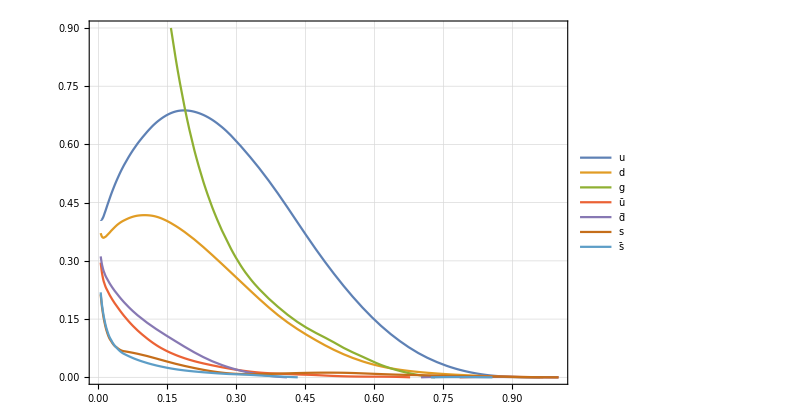

```mathematica
(* Plot xPDF : Peskin pg 563 *)
uppdf=xPDFcv[x,4,2];  (* Peak height is different from the Peskin *)
downpdf=xPDFcv[x,4,1];
gluepdf=xPDFcv[x,4,0];
upbarpdf=xPDFcv[x,4,-2];
dbarpdf=xPDFcv[x,4,-1];
spdf=xPDFcv[x,4,3];
sbarpdf=xPDFcv[x,4,-3];   
Plot[{uppdf,downpdf,gluepdf,upbarpdf,dbarpdf,spdf,sbarpdf},{x,0.005,1},PlotRange->{{0,1},{0,0.9}},PlotLegends->{"u","d","g","ū","d̄","s","s̄"}]
```

```mathematica
Definitions;

ecoll=13000;
scoll=ecoll^2;


(*pdf[x_,Q_,flav_]:=If[x≤1.0&&x>10^-9&&xPDFcv[x,Q^2,flav]>0,1/x xPDFcv[x,Q^2,flav],0]*)
pdf[x_,flav_]:=xPDFcv[x,mz^2,flav]/.mz->91.1876/.mw->80.387

(* remember: quarkID = 2 (up), 1 (down),   gluon = 0 *)

udbarpdf=2/M(pdf[M/(√scoll)Exp[Y],2]pdf[M/(√scoll)Exp[-Y],-1]+pdf[M/(√scoll)Exp[Y],-1]pdf[M/(√scoll)Exp[-Y], 2]);
```

### Proton Level Calculation

#### dσ/dM Calculation

```mathematica
dσdCθwil = dσhatdCθ;
partonicσ[n_]:=Integrate[SeriesCoefficient[dσdCθwil,{x,0,n}],{Cθ,-1,1}]/.{Ein->M/2}//Simplify
```

```mathematica
variableSM=partonicσ[0]
```

(39120.6 M^2)/(M^4-12924.1 M^2+4.17854×10^7)

```mathematica
variablelistOx = DeleteDuplicates@Cases[partonicσ[1],_Symbol,Infinity];
variablelistOx=Delete[variablelistOx,{{1}}]
dσdMOxterm=Table[Coefficient[partonicσ[1],variablelistOx[[wilson]]],{wilson,1,Length[variablelistOx]}]
```

{CHL36til,CHQ36til,CLQ36til,δGF6}

{(5.16469×10^6 M^2 (0.0151493 M^4-195.791 M^2+632744.))/((M^4-12924.1 M^2+4.17854×10^7)^2),(5.16469×10^6 M^2 (0.0151493 M^4-195.791 M^2+632471.))/((M^4-12924.1 M^2+4.17854×10^7)^2),(5.16469×10^6 M^2 (2.34433×10^-6 M^6-0.0454478 M^4+293.75 M^2-633017.))/((M^4-12924.1 M^2+4.17854×10^7)^2),(5.16469×10^6 M^2 (-0.0214243 M^4+276.89 M^2-894642.))/((M^4-12924.1 M^2+4.17854×10^7)^2)}

```mathematica
σpp2lνSM=1/10^5 Vegas[10^5 variableSM udbarpdf,{M,1,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 10000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal-> 3,AccuracyGoal->3, Verbose-> 0]
```

Vegas::success: Needed 1000000 function evaluations.

(8180.47 | 4.16886 | 1.53355×10^-9)

```mathematica
σpp2lνOx={};
Monitor[Do[
protonσ=1/10^5 Vegas[10^5 dσdMOxterm[[i]]udbarpdf,{M,1,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 10000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal-> 3,AccuracyGoal->3, Verbose-> 0];
AppendTo[σpp2lνOx,{ variablelistOx[[i]],protonσ}],{i,1,Length[variablelistOx]}],i];
σpp2lνOx
```

Vegas::success: Needed 700000 function evaluations.

Vegas::success: Needed 2200000 function evaluations.

Vegas::accuracy: Desired accuracy was not reached within 10450000 function evaluations.

Vegas::success: Needed 700000 function evaluations.

General::stop: Further output of Vegas::success will be suppressed during this calculation.

(CHL36til | (10893.2 | 10.4734 | 1.5155×10^-9)
CHQ36til | (5425.03 | 4.66252 | 5.69339×10^-15)
CLQ36til | (23.7503 | 0.415993 | 0.)
δGF6 | (-11539. | 10.7948 | 5.46989×10^-10))

```mathematica
variablelistOx2={CLQs38til,CHud6til^2,CHD8til,CHD28til,CHQ38til,CHL38til,CHQ36til^2,CHL36til^2,CHQ36til CHL36til,CHL36til CLQ36til,CHQ36til CLQ36til,CHLQ28til,CHLQ58til,CLQ36til^2,CLQt38til, δGF6^2,CHL36til δGF6,CHQ36til δGF6,δGF6 CLQ36til,δGF8}
dσdMOx2term=Table[Coefficient[partonicσ[2],variablelistOx2[[wilson]]],{wilson,1,Length[variablelistOx2]}]
```

{CLQs38til,CHud6til^2,CHD8til,CHD28til,CHQ38til,CHL38til,CHQ36til^2,CHL36til^2,CHL36til CHQ36til,CHL36til CLQ36til,CHQ36til CLQ36til,CHLQ28til,CHLQ58til,CLQ36til^2,CLQt38til,δGF6^2,CHL36til δGF6,CHQ36til δGF6,CLQ36til δGF6,δGF8}

{(8.2635×10^7 M^2 (-1.20844×10^-12 M^12+3.9045×10^-8 M^10-0.000504689 M^8+3.26218 M^6-10544.3 M^4+1.36347×10^7 M^2))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (0.000118354 M^8-3.05924 M^6+29655.6 M^4-1.27776×10^8 M^2+2.06469×10^11))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (-0.000236707 M^8+6.11847 M^6-59313.4 M^4+2.5558×10^8 M^2-4.13027×10^11))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (0.000236707 M^8-6.11847 M^6+59313.4 M^4-2.5558×10^8 M^2+4.13027×10^11))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (0.000473414 M^8-12.2369 M^6+118622. M^4-5.11105×10^8 M^2+8.25877×10^11))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (0.000473414 M^8-12.2369 M^6+118631. M^4-5.11215×10^8 M^2+8.26233×10^11))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (0.000473414 M^8-12.2369 M^6+118531. M^4-5.09928×10^8 M^2+8.22075×10^11))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (0.000473414 M^8-12.2369 M^6+118591. M^4-5.107×10^8 M^2+8.2457×10^11))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (0.00189366 (M^4-12924.1 M^2+4.17854×10^7)^2-125.17 (M^4-12924.1 M^2+4.17854×10^7)+2.46159×10^6))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (1.46521×10^-7 (M^2-6462.07) (M^4-12924.1 M^2+4.17854×10^7)^2-0.00528271 (1. M^2-6462.07) (M^4-12924.1 M^2+4.17854×10^7)))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (1.46521×10^-7 (M^2-6462.07) (M^4-12924.1 M^2+4.17854×10^7)^2-0.0105654 (1. M^2-6462.07) (M^4-12924.1 M^2+4.17854×10^7)))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (7.32604×10^-8 M^10-0.00236707 M^8+30.5963 M^6-197767. M^4+6.39239×10^8 M^2-8.2659×10^11))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (7.32604×10^-8 M^10-0.00236707 M^8+30.5963 M^6-197767. M^4+6.39239×10^8 M^2-8.2659×10^11))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (1.1337×10^-11 M^12-4.39563×10^-7 M^10+0.00710213 M^8-61.2085 M^6+296765. M^4-7.67485×10^8 M^2+8.27125×10^11))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (3.02109×10^-13 M^12-9.76126×10^-9 M^10+0.000126172 M^8-0.815545 M^6+2636.08 M^4-3.40867×10^6 M^2))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (0.00284048 M^8-73.4216 M^6+711658. M^4-3.06564×10^9 M^2+4.95205×10^12))/((M^4-12924.1 M^2+4.17854×10^7)^3),1/((M^4-12924.1 M^2+4.17854×10^7)^3)8.2635×10^7 M^2 (6.75737×10^-19 (M^4-12924.1 M^2+4.17854×10^7)^2-0.00267803 (1. M^4-12924.1 M^2+4.17583×10^7) (M^4-12924.1 M^2+4.17854×10^7)+96.5547 (M^4-12924.1 M^2+4.17854×10^7)-2.61091×10^6),1/((M^4-12924.1 M^2+4.17854×10^7)^3)8.2635×10^7 M^2 (6.75737×10^-19 (M^4-12924.1 M^2+4.17854×10^7)^2-0.00267803 (1. M^4-12924.1 M^2+4.17583×10^7) (M^4-12924.1 M^2+4.17854×10^7)+193.109 (M^4-12924.1 M^2+4.17854×10^7)-5.22182×10^6),(8.2635×10^7 M^2 (4.12437×10^-23 (M^2-6462.07) (M^4-12924.1 M^2+4.17854×10^7)^2-4.14424×10^-7 (1. M^2-6462.07) (M^4-12924.1 M^2+4.17854×10^7) (1. M^4-12924.1 M^2+4.17583×10^7)))/((M^4-12924.1 M^2+4.17854×10^7)^3),(8.2635×10^7 M^2 (-0.00133902 M^8+34.6113 M^6-335527. M^4+1.44578×10^9 M^2-2.33644×10^12))/((M^4-12924.1 M^2+4.17854×10^7)^3)}

```mathematica
σpp2lνOx2={};
Monitor[Do[
protonσ=1/10^5 Vegas[10^5 dσdMOx2term[[i]]udbarpdf,{M,1,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 10000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal-> 3,AccuracyGoal->3, Verbose-> 0];
AppendTo[σpp2lνOx2,{ variablelistOx2[[i]],protonσ}],{i,1,Length[variablelistOx2]}],i];
σpp2lνOx2
```

Vegas::success: Needed 1000000 function evaluations.

Vegas::success: Needed 2200000 function evaluations.

Vegas::success: Needed 700000 function evaluations.

General::stop: Further output of Vegas::success will be suppressed during this calculation.

Vegas::accuracy: Desired accuracy was not reached within 10450000 function evaluations.

General::stop: Further output of Vegas::accuracy will be suppressed during this calculation.

(CLQs38til | (-293.575 | 0.233377 | 1.38764×10^-10)
CHud6til^2 | (678.129 | 0.582815 | 5.69338×10^-15)
CHD8til | (-2039.83 | 1.90826 | 5.46989×10^-10)
CHD28til | (2039.83 | 1.90826 | 5.46989×10^-10)
CHQ38til | (2712.52 | 2.33126 | 5.69338×10^-15)
CHL38til | (5446.62 | 5.23671 | 1.5155×10^-9)
CHQ36til^2 | (-4581.59 | 4.35667 | 1.78361×10^-12)
CHL36til^2 | (-1845.17 | 1.84473 | 0.)
CHL36til CHQ36til | (14492.7 | 13.0481 | 4.80814×10^-8)
CHL36til CLQ36til | (27.0342 | 0.362601 | 1.11022×10^-21)
CHQ36til CLQ36til | (30.3153 | 0.36172 | 0.)
CHLQ28til | (11.8751 | 0.207997 | 0.)
CHLQ58til | (11.8751 | 0.207997 | 0.)
CLQ36til^2 | (2747.56 | 1.99259 | 2.8753×10^-9)
CLQt38til | (73.3938 | 0.0583443 | 1.38764×10^-10)
δGF6^2 | (16271.3 | 16.1466 | 2.66586×10^-8)
CHL36til δGF6 | (-15340.8 | 15.2231 | 2.66586×10^-8)
CHQ36til δGF6 | (-7604.12 | 7.46798 | 5.08886×10^-14)
CLQ36til δGF6 | (-74.1395 | 1.05571 | 0.)
δGF8 | (-11539. | 10.7948 | 5.46989×10^-10))

```mathematica
intSM=σpp2lνSM[[1,1]]
int1=Table[σpp2lνOx[[i,2,1,1]],{i,1,Length[σpp2lνOx]}]
int2=Table[σpp2lνOx2[[i,2,1,1]],{i,1,Length[σpp2lνOx2]}]
```

8180.47

{10893.2,5425.03,23.7503,-11539.}

{-293.575,678.129,-2039.83,2039.83,2712.52,5446.62,-4581.59,-1845.17,14492.7,27.0342,30.3153,11.8751,11.8751,2747.56,73.3938,16271.3,-15340.8,-7604.12,-74.1395,-11539.}

```mathematica
SeriesCoefficient[1/intSM(intSM+int1.variablelistOx x+int2.variablelistOx2 x^2),{x,0,1}]//Expand
SeriesCoefficient[1/intSM(intSM+int1.variablelistOx x+int2.variablelistOx2 x^2),{x,0,2}]//Expand
```

1.33161 CHL36til+0.663169 CHQ36til+0.00290329 CLQ36til-1.41056 δGF6

0.249354 CHD28til-0.249354 CHD8til-0.225558 CHL36til^2+1.77162 CHL36til CHQ36til+0.00330473 CHL36til CLQ36til-1.87529 CHL36til δGF6+0.665807 CHL38til+0.00145164 CHLQ28til+0.00145164 CHLQ58til-0.560065 CHQ36til^2+0.00370581 CHQ36til CLQ36til-0.929545 CHQ36til δGF6+0.331584 CHQ38til+0.0828961 CHud6til^2+0.335868 CLQ36til^2-0.00906298 CLQ36til δGF6-0.0358873 CLQs38til+0.00897183 CLQt38til+1.98905 δGF6^2-1.41056 δGF8

```mathematica
(* Tae *)int1.{c36HψL,c36Hψq,cLQ3,δGF6}
```

10893.2 c36HψL+5425.03 c36Hψq+23.7503 cLQ3-11539. δGF6

```mathematica
(* Adam *)10893.6 c36HψL+5427.44 c36Hψq+5.93712 cLQ3-11540.6 δGF6
```

10893.6 c36HψL+5427.44 c36Hψq+5.93712 cLQ3-11540.6 δGF6

```mathematica
(* Tae *)int2.{c8LQ3s,cHud6^2,c8HD,c8HD2,c38Hψq,c38HψL,c36Hψq^2,c36HψL^2,c36Hψq c36HψL,c36HψL cLQ3,c36Hψq cLQ3,c8LQ2,c8LQ5,cLQ3^2,c8LQ3t, δGF6^2,c36HψL δGF6,c36Hψq δGF6,δGF6 cLQ3,δGF8}
```

-1845.17 c36HψL^2+14492.7 c36HψL c36Hψq+6.75856 c36HψL cLQ3-15340.8 c36HψL δGF6-4581.59 c36Hψq^2+7.57882 c36Hψq cLQ3-7604.12 c36Hψq δGF6+5446.62 c38HψL+2712.52 c38Hψq-2039.83 c8HD+2039.83 c8HD2+2.96878 c8LQ2-73.3938 c8LQ3s+18.3485 c8LQ3t+1.48439 c8LQ5+678.129 cHud6^2+171.723 cLQ3^2-18.5349 cLQ3 δGF6+16271.3 δGF6^2-11539. δGF8

```mathematica
(* Adam *)171.71  (-10.7163 c36HψL^2+84.4688 c36HψL c36Hψq+0.0393512 c36HψL cLQ3-89.4335 c36HψL δGF6-26.6108 c36Hψq^2+0.044126 c36Hψq cLQ3-44.4456 c36Hψq δGF6+31.721 c38HψL+15.8042 c38Hψq-11.8813 c8HD+11.8813 c8HD2+0.0172882 c8LQ2-0.427397 c8LQ3s+0.106849 c8LQ3t+0.00864412 c8LQ5+3.95105 cHud6^2+1. cLQ3^2-0.107926 cLQ3 δGF6+94.8586 δGF6^2-67.2107 δGF8)//Expand
```

-1840.1 c36HψL^2+14504.1 c36HψL c36Hψq+6.75699 c36HψL cLQ3-15356.6 c36HψL δGF6-4569.34 c36Hψq^2+7.57688 c36Hψq cLQ3-7631.75 c36Hψq δGF6+5446.81 c38HψL+2713.74 c38Hψq-2040.14 c8HD+2040.14 c8HD2+2.96856 c8LQ2-73.3883 c8LQ3s+18.347 c8LQ3t+1.48428 c8LQ5+678.435 cHud6^2+171.71 cLQ3^2-18.532 cLQ3 δGF6+16288.2 δGF6^2-11540.7 δGF8